```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2+c03 x^3+c04 x^4, 0≤x≤1}, {c11(x-1)+c12(x-1)^2+c13(x-1)^3+c14(x-1)^4, 1<x≤2}, {c21(x-2)+c22(x-2)^2+c23(x-2)^3+c24(x-2)^4, 2<x≤3}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
I3=f[3]
```

1+c01+c02+c03+c04

c11+c12+c13+c14

c21+c22+c23+c24

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[f[x+2]+f[x+1]+f[x]+f[x-1]+f[x-2]+f[x-3],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[-2f[x+2]-f[x+1]+f[x-1]+2f[x-2]+3f[x-3],x>0&&x<1],x]
```

{2+c01+c02+c03+c04+c11+c12+c13+c14+c21+c22+c23+c24,-2 c02-3 c03-4 c04-2 c12-3 c13-4 c14-2 c22-3 c23-4 c24,2 c02+3 c03+4 c04+2 c12+3 c13+4 c14+2 c22+3 c23+4 c24+2 (c04+c14+c24),-4 (c04+c14+c24),2 (c04+c14+c24)}

{1+c01+c02+c03+c04+2 c11+2 c12+2 c13+2 c14+3 c21+3 c22+3 c23+3 c24,-c01-2 c02-3 c03-4 c04-3 c11-4 c12-6 c13-8 c14-5 c21-6 c22-9 c23-12 c24,c02+3 c03+6 c04+c12+6 c13+12 c14+c22+9 c23+18 c24,-c03-4 c04-3 c13-8 c14-5 c23-12 c24,c04+c14+c24}

```mathematica
(*Smoothness*)
Df=Simplify[D[f[x],x],x>0]/.Abs'[x]->1
c01+x (2 c02+x (3 c03+4 c04 x))/.x->1
c11+(2 c12+(3 c13+4 c14 (-1+x)) (-1+x)) (-1+x)/.x->1
c11+(2 c12+(3 c13+4 c14 (-1+x)) (-1+x)) (-1+x)/.x->2
c21+(2 c22+(3 c23+4 c24 (-2+x)) (-2+x)) (-2+x)/.x->2
c21+(2 c22+(3 c23+4 c24 (-2+x)) (-2+x)) (-2+x)/.x->3
```

Piecewise[{{c01+x (2 c02+x (3 c03+4 c04 x)), x≤1}, {c11+(2 c12+(3 c13+4 c14 (-1+x)) (-1+x)) (-1+x), 1<x≤2}, {c21+(2 c22+(3 c23+4 c24 (-2+x)) (-2+x)) (-2+x), 2<x≤3}, {0, True}}]

c01+2 c02+3 c03+4 c04

c11

c11+2 c12+3 c13+4 c14

c21

c21+2 c22+3 c23+4 c24

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	I3==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0,
	T1[[4]]==0,
	c01==0,
	c01+2 c02+3 c03+4 c04==c11,
	c11+2 c12+3 c13+4 c14==c21,
	c21+2 c22+3 c23+4 c24==0
	},
	{c01,c02,c03,c04,c11,c12,c13,c14,c21,c22,c23,c24}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c01→0,c04→-1-c02-c03,c11→-4-2 c02-c03,c13→41/4+5 c02+(5 c03)/2-2 c12,c14→-25/4-3 c02-(3 c03)/2+c12,c21→7/4+c02+c03/2,c22→15/4+2 c02+(3 c03)/2-c12,c23→-51/4-7 c02-(9 c03)/2+2 c12,c24→29/4+4 c02+(5 c03)/2-c12}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-5)^6 ∑_(j=-5)^6 W1[i-j]f[x-i,y-j]/.GenSol;
{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}=Parallelize[{
	Simplify[SumF1,x>0&&x<1&&y>0&&y<1],
	Simplify[SumF1,x>0&&x<1&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>2&&y<3],
	Simplify[SumF1,x>-2&&x<-1&&y>2&&y<3],
	Simplify[SumF1,x>-2&&x<-1&&y>3&&y<4]
}];
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1a4,DSumF1a5,DSumF1a6}=Parallelize[{
	FullSimplify[D[SumF1a1,{{x,y}}]],
	FullSimplify[D[SumF1a2,{{x,y}}]],
	FullSimplify[D[SumF1a3,{{x,y}}]],
	FullSimplify[D[SumF1a4,{{x,y}}]],
	FullSimplify[D[SumF1a5,{{x,y}}]],
	FullSimplify[D[SumF1a6,{{x,y}}]]
}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}=Parallelize[{
	Simplify[SumF1,x>1&&x<2&&y>0&&y<1],
	Simplify[SumF1,x>1&&x<2&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-2&&y<-1],
	Simplify[SumF1,x>3&&x<4&&y>-2&&y<-1],
	Simplify[SumF1,x>3&&x<4&&y>-3&&y<-2]
}];
{DSumF1b1,DSumF1b2,DSumF1b3,DSumF1b4,DSumF1b5,DSumF1b6}=Parallelize[{
	FullSimplify[D[SumF1b1,{{x,y}}]],
	FullSimplify[D[SumF1b2,{{x,y}}]],
	FullSimplify[D[SumF1b3,{{x,y}}]],
	FullSimplify[D[SumF1b4,{{x,y}}]],
	FullSimplify[D[SumF1b5,{{x,y}}]],
	FullSimplify[D[SumF1b6,{{x,y}}]]
}];
```

```mathematica
DSumF1a1=Simplify[DSumF1a1/.φ->1/2];
DSumF1a2=Simplify[DSumF1a2/.φ->1/2];
DSumF1a3=Simplify[DSumF1a3/.φ->1/2];
DSumF1a4=Simplify[DSumF1a4/.φ->1/2];
DSumF1a5=Simplify[DSumF1a5/.φ->1/2];
DSumF1a6=Simplify[DSumF1a6/.φ->1/2];
DSumF1b1=Simplify[DSumF1b1/.φ->1/2];
DSumF1b2=Simplify[DSumF1b2/.φ->1/2];
DSumF1b3=Simplify[DSumF1b3/.φ->1/2];
DSumF1b4=Simplify[DSumF1b4/.φ->1/2];
DSumF1b5=Simplify[DSumF1b5/.φ->1/2];
DSumF1b6=Simplify[DSumF1b6/.φ->1/2];
```

```mathematica
{Err1a1,Err1a2,Err1a3,Err1a4,Err1a5,Err1a6}=Parallelize[{
	Simplify[∫_0^1 ∫_0^1 (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_0^1 (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_-1^0 (DSumF1a3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_2^3 ∫_-1^0 (DSumF1a4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_2^3 ∫_-2^-1 (DSumF1a5.{1,1})^2 ⅆxⅆy],
	Simplify[∫_3^4 ∫_-2^-1 (DSumF1a6.{1,1})^2 ⅆxⅆy]
}];
{Err1b1,Err1b2,Err1b3,Err1b4,Err1b5,Err1b6}=Parallelize[{
	Simplify[∫_0^1 ∫_1^2 (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_1^2 (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_2^3 (DSumF1b3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-2^-1 ∫_2^3 (DSumF1b4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-2^-1 ∫_3^4 (DSumF1b5.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-3^-2 ∫_3^4 (DSumF1b6.{1,1})^2 ⅆxⅆy]
}];
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1a4+Err1a5+Err1a6+Err1b1+Err1b2+Err1b3+Err1b4+Err1b5+Err1b6];
```

```mathematica
Err=FullSimplify[Err1]
DErr=FullSimplify[D[Err,{{c02,c03,c12}}]];
H=FullSimplify[D[Err,{{c02,c03,c12},2}]];
Sols=Solve[DErr==0,{c02,c03,c12}];
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1/541900800(710720512 c02^4+64 c02^3 (96603491+22528790 c03-4600728 c12)+16 c02^2 (1265098369+68874844 c03^2+c03 (581444444-28506576 c12)+96 c12 (-1193613+33406 c12))+3 (5110913111-916196400 c12+8 (c03 (604723137+c03 (211536105+32705908 c03+2023278 c03^2))-6 c03 (13769049+4 c03 (818366+72175 c03)) c12+8 (1121269+525692 c03+75788 c03^2) c12^2-1024 (297+98 c03) c12^3+6656 c12^4))+12 c02 (2419537509+31366520 c03^3+4 c03^2 (97444621-4942360 c12)-8 c12 (40513703+16 c12 (-130313+2832 c12))+2 c03 (843003883+64 c12 (-1211445+35278 c12))))

1 | 0.0497664 | True
2 | -43542.+77568.6 ⅈ | False
3 | -43542.-77568.6 ⅈ | False
4 | 157568.+6242.88 ⅈ | False
5 | 157568.-6242.88 ⅈ | False
6 | -18159.3+14818.5 ⅈ | False
7 | -18159.3-14818.5 ⅈ | False
8 | -212.426+699.396 ⅈ | False
9 | -212.426-699.396 ⅈ | False
10 | 0.850573+0.379191 ⅈ | False
11 | 0.850573-0.379191 ⅈ | False
12 | 3875.75+1429.82 ⅈ | False
13 | 3875.75-1429.82 ⅈ | False
14 | 1.703-0.711495 ⅈ | False
15 | 1.703+0.711495 ⅈ | False
16 | 0.378762+0.0717344 ⅈ | False
17 | 0.378762-0.0717344 ⅈ | False
18 | -15600.3-70685.4 ⅈ | False
19 | -15600.3+70685.4 ⅈ | False
20 | 0.3265+0.0360115 ⅈ | False
21 | 0.3265-0.0360115 ⅈ | False
22 | 2.85639+0.891125 ⅈ | False
23 | 2.85639-0.891125 ⅈ | False
24 | 111126.-56909.7 ⅈ | False
25 | 111126.+56909.7 ⅈ | False
26 | 20209.6+6622.78 ⅈ | False
27 | 20209.6-6622.78 ⅈ | False

{c01→0.,c04→0.309774,c11→-0.838313,c13→0.958096,c14→-0.813626,c21→0.169156,c22→0.165539,c23→-0.838547,c24→0.503852,c02→-1.85191,c03→0.54214,c12→0.69384}

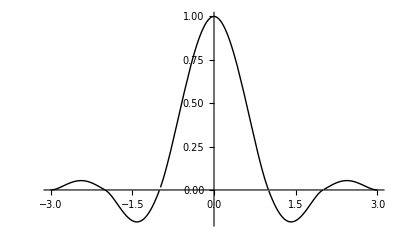

```mathematica
Sol=Sols[[1]];(*Huge*)
FullSol=N[Join[GenSol/.Sol,Sol]]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```